```mathematica
A:=1;
Subscript[ω, p]=1;
z:=1;
x:=1;
θ:=Pi/3;
Subscript[Δ, t]:=100;
c:=1;
A*Cos[(Subscript[ω, p]/c)*(Sin[θ]*x+Cos[θ]*z)-Subscript[ω, p]*Subscript[t, p]]Exp[-(((Sin[θ]*x+Cos[θ]*z)/Subscript[ω, p]-Subscript[t, p])/Subscript[Δ, t])^2]
```

ⅇ^(-(1/2+(√3)/2-t_p)^2/10000) Cos[1/2+(√3)/2-t_p]

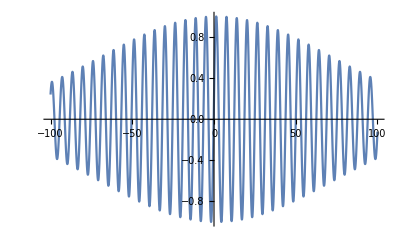

ⅇ^(-(1/2+(√3)/2-t_p)^2/10000) Sin[1/2+(√3)/2-t_p]+(ⅇ^(-(1/2+(√3)/2-t_p)^2/10000) Cos[1/2+(√3)/2-t_p] (1/2+(√3)/2-t_p))/5000

```mathematica
Plot[%101,{Subscript[t, p],-100,100}]
D[%101,Subscript[t, p]]
```

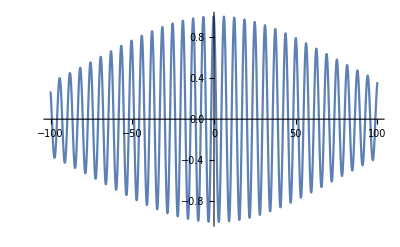

```mathematica
Plot[%110,{Subscript[t, p],-100,100}]
```